```mathematica
it = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ)∫_(d/2 - a/2)^(d/2+a/2) E^((2 π I (w-y1)^2)/(2 * D1 * λ))*E^((2 π I (y1-z)^2)/(2 * D2 * λ))ⅆy1;
ib = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ) ∫_(-d/2-a/2)^(-d/2+a/2) E^((2 π I (w-y2)^2)/(2 * D1 * λ))*E^((2 π I (y2-z)^2)/(2 * D2 * λ))ⅆy2;
```

```mathematica
i = (it + ib);
coni = Conjugate[i];
func = i*coni;
```

```mathematica
D1 = 380;
D2 = 500;
λ = .000546;
z = x -6.4;
d = .353;
a = .1;
```

```mathematica
func;
realfunc = 8500*Re[func];
```

```mathematica
SetDirectory["/Users/danikaluntz-martin/Desktop/Advanced Lab/DoubleSlit-ED"];
counts3 = Import["20141122_double_slit_bulb_counts3.csv"];
counts3;
```

```mathematica
fit3 = NonlinearModelFit[counts3,realfunc,{{w,0}}, x];
```

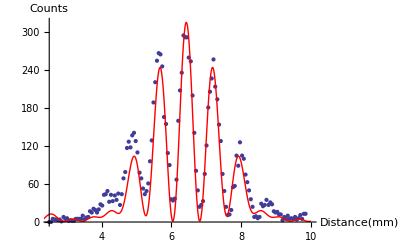

```mathematica
plot3 = Plot[fit3[x], {x, 0, 10},PlotRange->All,PlotStyle -> Red];
Show[ListPlot[counts3], plot3, AxesLabel-> {Distance [mm], Counts},PlotRange-> {{2.5,10},All}]
```

```mathematica
ChiSq3=∑_(j=1)^145 ((fit3["FitResiduals"][[j]])/(2(√counts3[[j,2]]-√1.68)))^2
RedChiSq3= ChiSq3/7
```

857.116

122.445